# GH, SHEL and OIF Shifts: Single Interface M. T. Lusk Last Edited: August 30, 2016

-Graphics-

## Plotting Tools

```mathematica
Clear[font,coloredfont];
font[name_,size_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold]

coloredfont[name_,size_,color_]:=Style[name,FontFamily->"Helvetica",FontSize->size,Bold, color]
```

## Theory

### Basic Theory of Modal Representation of the E-Field

References:

[1] An angular spectrum representation approach to the Goos-Hanchen shift, M. McGuirk and C. K. Carniglia, J.Opt. Soc. Am. Vol 67(1) p 103 1977 [Spectral_Decomposition_McGuirk_JOSA_1977.pdf]

[2] Optical Coherence and Quantum Optics, Mandel and Wolf [Quantum_Optics_Mandel_Wolf.pdf]

McGuirk gives the key result and some hints about the proof, while Mandel gives a step-by-step detailed proof. See Mandel p111 Eq 3.2-12. This is the derivation repeated below.

Consider a beam characterized by

E⃗[r⃗,t]=E[r⃗] f ⅇ^(ⅈ(k_0·r- ω t))

Here f is the fixed polarization of the beam. This is a monchromatic beam since there is only 1 temporal frequency, ω. Since k_0=k_0 κ_0, we immediately have that k_0=ω/c. The beam can be decomposed into plane waves via a Fourier transform, but the magnitude of each wave vector must be k_0 because both the speed and temporal frequency are fixed. Thus, the E-field can be described in terms of a spectrum of mono-length wave vectors:

k=k_0 κ.

Suppose our incident beam, traveling with central wave vector, k_0, makes an angle of θ with a planar interface with unit normal, n̂.

It will be convenient to define the beam frame, which is fixed once θ is prescribed. Let u_3 be the unit vector along the beam axis. Then

u_2= n×u_3

u_1= u_2×u_3

Note that (û)_2 is normal to the plane of incidence (which is the plane containing (û)_3 and n̂), so E-fields in this direction are TE (s-polarized). Therefore E-fields in the (û)_1 direction are TM (p-polarized). The polarization of the beam is then

f= f_1 u_1+f_2 u_2.

Coordinates along each beam axis will be referred to as x, y, and z respectively.

Suppose that |k|=k_0. This implies that

k= k_0(κ_x u_1 +κ_y u_2  + √(1-κ_x^2-κ_y^2)u_3).

Consider the z = z_0 plane, where z_0 is completely arbitrary, and define the angular spectrum, Ẽ[κ_x,κ_y;z_0], as:

Ẽ[κ_x,κ_y;z_0]=∫∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(-ⅈ κ_y y').

Then, as shown below,

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yẼ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y)

Note that we can and have dropped the subscript on z.

Proof:

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ k_xⅆ k_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(ⅈ κ_x x)ⅇ^(-ⅈ κ_y y')ⅇ^(ⅈ κ_y y)

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ κ_xⅆ κ_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(ⅈ κ_x(x-x'))ⅇ^(ⅈ κ_y(y-y'))

E[x,y,z_0]= ∫ⅆx'ⅆy' E[x',y',z_0]δ[x-x']δ[y-y']

E[x,y,z_0]= E[x,y,z_0]

This result can be used to construct a general spectral representation of the E-field. First note that

(∇^2 +κ^2)E[r]=0

Substitute our Fourier expression into this Helmholtz equation and reverse the order of integration and differentiation:

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y(∇^2 +κ^2)(Ẽ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y((-κ_x^2-κ_y^2+1+∂_zz)Ẽ[κ_x,κ_y;z])ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

Since this holds for all values of x and y, the integrand must be zero implying that

(∂_zz + κ_z^2)Ẽ[κ_x,κ_y;z]=0

The general solution to this equation is

Ẽ[κ_x,κ_y;z]= A[κ_x,κ_y]ⅇ^(ⅈ κ_z z)+B[κ_x,κ_y]ⅇ^(-ⅈ κ_z z)

Substitution of this result into the expression for E gives

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yA[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y +κ_z z))+(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yB[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y-κ_z z))

This is not a Fourier decomposition of the beam. Rather, it is a modal representation of the beam that only superficially resembles a Fourier transform.

The final expression is

E(r)≡E(r)f= (∑_(λ=1,2) u_λ f_λ)∫∫∫ⅆ k_xⅆ k_yⅆ k_z Ẽ(k)ⅇ^(ⅈ(k·r))

### Derivation of Reflected E-field

The unit normal of the plane is

n= -Sin[θ]u_1+Cos[θ]u_3

κ ... the normalized wave vector for each plane wave element of the incident beam. The coordinate basis chosen {u_1, u_2, u_3}, is that of the beam with the plane of incidence that which contains interface normal, n, and u_3.

u_(1') ... TM/1/p polarization of an individual plane wave element
u_(2') ... TE/2/s polarization of an individual plane wave element
u_(3') ... direction of propagation of an individual plane wave element

Construct a set of linearized relations in which the primed basis vectors are expressed in terms of the beam basis vectors. (Eq 19 of Bliokh PRE 2007).

```mathematica
Clear[κvec,κx,κy,κz,e1,e2];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

nvec = {-Sin[θ],0,Cos[θ]};

u2prime= Cross[nvec,κvec]/(√(Cross[nvec,κvec].Cross[nvec,κvec]));

u1prime  =Simplify[ Cross[u2prime,κvec]/(√(Cross[u2prime,κvec].Cross[u2prime,κvec]))];

u1prime=FullSimplify[Expand[Normal[Series[u1prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u2prime=FullSimplify[Expand[Normal[Series[u2prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u3prime= Cross[u1prime,u2prime]/.{κx^2->0,κy^2->0,κx κy->0}
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

{κx,κy,1}

The physical polarization of each plane wave element is taken to be the same as that of the beam, so the polarization does not change from plane wave to plane wave. Instead, the electric field of each plane wave is expressed in terms of the Fourier transform of the scalar E-field of the beam. Call this Ẽ so that

E=E e

Ẽ=ℱ[E]

Ẽ=Ẽ e = Ẽ (f_1 u_1+f_2 u_2)

where f is the polarization vector of the beam.

But we can also write

Ẽ=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') + (Ẽ)_z' u_(3')

Since

u_(1')=u_1+κ_y Cot[θ]u_2-κ_x u_3

u_(2')=-κ_y Cot[θ]u_1+u_2-κ_y u_3

u_(3')=κ_x u_1+κ_y u_2+u_3

Now invert these equations to obtain the unprimed basis vectors in terms of their primed counterparts.

```mathematica
sol=Simplify[Solve[{
u1p == {u1,u2,u3}.u1prime ,
u2p =={u1,u2,u3}.u2prime,
u3p =={u1,u2,u3}.u3prime
},{u1,u2,u3}]];

Expand[sol] /. {κx^2->0,κy^2->0,κx κy->0}
```

{{u1→u1p+u3p κx-u2p κy Cot[θ],u2→u2p+u3p κy+u1p κy Cot[θ],u3→u3p-u1p κx-u2p κy}}

We have two ways of writing the E-field:

Ẽ= Ẽ (f_1 u_1+f_2 u_2)=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2')

Using the relations derived above, equate the components.

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1(u_(1')-κ_y Cot[θ]u_(2')+κ_x u_(3'))+ f_2(κ_y Cot[θ]u_(1')+u_(2')+κ_y u_(3')))

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1+f_2 κ_y Cot[θ])u_(1')+Ẽ (f_2-f_1 κ_y Cot[θ])u_(2') + Ẽ (f_1 κ_x+f_2 κ_y)u_(3'))

This implies that

(Ẽ)_x' =Ẽ (f_1+f_2 κ_y Cot[θ])

(Ẽ)_y' =Ẽ (f_2-f_1 κ_y Cot[θ])

It also leaves a u_(3') component that sums to zero when all plane waves are taken into account.

Not surprisingly, we can recover our original formulation of the incident field:

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

{Etildemag f1,Etildemag f2,Etildemag (-f1 κx-f2 κy)}

That is not the point though. We did this in order to be able to apply polarization-dependent reflection coefficients to each plane-wave vector.

The (Ẽ)_x' is multiplied by R_1, while the (Ẽ)_y' component is multiplied by R_2. We also need to constructed the primed unit vectors, here expressed in terms of the original incident angle although we could have put in θR directly. Later we will re-write the final result in terms of θR.

```mathematica
u1prime

u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
u1prime$R = u1prime/. {θ->π-θ}
u2prime$R = u2prime/. {θ->π-θ}
```

{1,-κy Cot[θ],-κx}

{κy Cot[θ],1,-κy}

```mathematica
Clear[u1prime$R,u2prime$R];

u1prime$R = u1prime
u2prime$R = u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

```mathematica
Clear[R1,R2];

Etilde$R = Simplify[Etildemag Expand[( f1 + κy Cot[π-θ] f2) u1prime$R (R1)+(f2 - κy Cot[π-θ]f1) u2prime$R R2] /. {κy^2->0,κx κy ->0}]
```

{Etildemag (f1 R1-f2 (R1+R2) κy Cot[θ]),Etildemag (f2 R2+f1 (R1+R2) κy Cot[θ]),-Etildemag (f1 R1 κx+f2 R2 κy)}

The final expression is therefore:

(Ẽ)_R= Ẽ((f_1 R_1-f_2 κ_y Cot[θ](R_1+R_2))u_1+(f_2 R_2 + f_1 κ_y Cot[θ](R_1+R_2 ))u_2-(f_1 R_1 κ_x + f_2 R_2  κ_y)u_3

Since the basis vectors are constant for a given beam, the reflected beam is easily recovered by just taking the inverse Fourier transform of each of its components above.

### Aside: Reflected Polarization Vector

As an aside, we also recover Bliokh’s polarization vector for plane wave elements of the reflected beam.

```mathematica
etildeR = Simplify[Expand[1/Etildemag Etilde$R ]/. {κy^2->0,κx κy ->0}]
```

{f1 R1-f2 (R1+R2) κy Cot[θR],f2 R2+f1 (R1+R2) κy Cot[θR],-f1 R1 κx-f2 R2 κy}

Replace f1 with 1, f2 with mc, and remember that Bliokh’s (m̃)^R ≡ m_c ρR. Then it clear that the line above is the same as Bliokh’s Eq 40 (below) once it is normalized.

-Graphics-

### Aside: Construction of Formulae for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1,R2,β,n];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(-n^2 Cos[β]+√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β_,n_]=FullSimplify[ArcTan[Re[R1 /. {κx->0,κy->0}],Im[R1 /. {κx->0,κy->0}]]];

Φ2[β_,n_]=FullSimplify[ArcTan[Re[R2 /. {κx->0,κy->0}],Im[R2 /. {κx->0,κy->0}]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))/(n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

((n^2 Cos[β]-ⅈ √(-n^2+Sin[β]^2)) (-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2)))/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

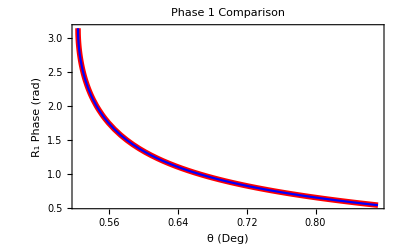

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

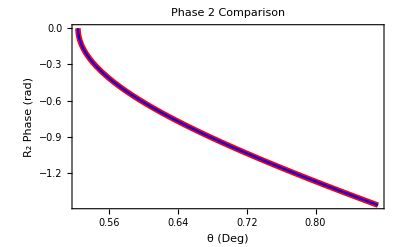

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

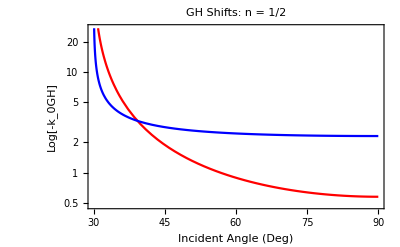

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

Here is the same plot but now in units for 600 nm incident light.

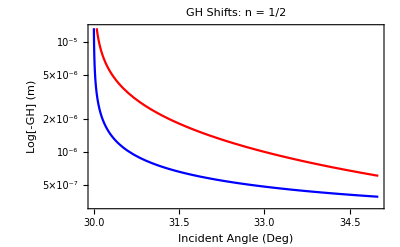

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

## Applications

### Construction of E-field in Paraxial Approximation: Must Run Each Time

r … radial distance from the center axis of the beam

z … axial distance from the beam’s focus (or “waist”)

z_R… Rayleigh Range, π w0^2/λ

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z) … radius of curvature of the beam’s wavefronts at z

ψ(z) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

```mathematica
Clear[Escalar,r,φfunc,z,w,w0,zR,λ,k,R,ψ,Nmax,Evec,k0];

ω = c1 k0;

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k0;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=Simplify[z(1 + (zR/z)^2)];

Nmax = 2 p+Abs[ℓ];

ψ[z_]=(Nmax+1)ArcTan[zR,z];


Escalar[x_,y_,z_]=Simplify[1/w[z] Exp[(-(x^2+y^2))/w[z]^2]Exp[-ⅈ (k0 (x^2+y^2)/(2 R[z])+ k0 z+ψ[z])]((r[x,y] √2)/w[z])^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ ℓ φfunc[x,y]],{Element[x,Reals],Element[y,Reals],Element[z,Reals]}];
```

```mathematica
Escalar2D[x_,y_]=FullSimplify[Escalar[x,y,0],{k0>0,w0>0}] /. w0 ->wk/k0
```

(2^(Abs[ℓ]/2) ⅇ^(-(k0^2 (x^2+y^2))/wk^2-ⅈ ℓ ArcTan[x,y]) k0 (k0/(wk √(1/(x^2+y^2))))^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2 k0^2 (x^2+y^2))/wk^2])/wk

### Key Fields: Must Run Each Time

```mathematica
Clear[κvec,κx,κy,κz];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

κvec0 = {0,0,1};

nvec = {-Sin[θ],0,Cos[θ]};
```

### Fresnel Coefficients: Must Run Each Time

```mathematica
Clear[R1,R2,β,n];

β =ArcCos[κvec.nvec];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[β]-√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)

T2=Simplify[(2Cos[β])/(Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: s/TE *)

T1=Simplify[(2n Cos[β])/(n^2 Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: p/TM *)
```

```mathematica
R1 /. {κx->0,κy->0}
```

(n^2 Cos[θ]-√(-1+n^2+Cos[θ]^2))/(n^2 Cos[θ]+√(-1+n^2+Cos[θ]^2))

```mathematica
θbrewster = ArcTan[n]
```

ArcTan[n]

```mathematica
Simplify[R1/. θ->θbrewster/. {κx->0,κy->0},{n>0}]

Simplify[R2/. θ->θbrewster/. {κx->0,κy->0},{n>0}]
```

0

(1-n^2)/(1+n^2)

```mathematica
θbrewster/Degree/. n->1.5168f
```

ArcTan[1.5168 f]/°

### Centroid Shifts versus Angle of Incidence: n = 1/1.5168, OAM = 0 (Glass/Air) FIG 4

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis: DON’T RUN THIS. It takes too long

```mathematica
Clear[plots,k0];

fontset = 6;

IFshift$tab$R1 = {};
IFshift$tab$R2 = {};
IFshift$tab$R3 = {};
IFshift$tab$R4 = {};
IFshift$tab$T1 = {};
IFshift$tab$T2 = {};
IFshift$tab$T3 = {};
IFshift$tab$T4 = {};

λ0 = 2 π;

dimset = 11;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 11;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;

Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

Print["Angle of Incidence: ",θloop,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];
Which[f$flag ==1, IFshift$T1={IFshift$Tx,IFshift$Ty},f$flag==2,IFshift$T2={IFshift$Tx,IFshift$Ty},f$flag==3,IFshift$T3={IFshift$Tx,IFshift$Ty},f$flag==4,IFshift$T4={IFshift$Tx,IFshift$Ty}];

},{f$flag,1,4}];

AppendTo[IFshift$tab$R1 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R1}];
AppendTo[IFshift$tab$R2 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R2}];
AppendTo[IFshift$tab$R3 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R3}];
AppendTo[IFshift$tab$R4 ,{ℓ /. params$here,θ/Degree /. params$here,IFshift$R4}];

Print["TE x (Reflected) = ",IFshift$R1," μm"]; 
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

Angle of Incidence: 10.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 12.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 14.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 16.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 18.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 20.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 22.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 24.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 26.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 28.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 30.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 32.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 34.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 36.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 38.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 40.°

TE x (Reflected) = {0,0} μm

Angle of Incidence: 42.°

TE x (Reflected) = {-2.47845,0} μm

Angle of Incidence: 44.°

TE x (Reflected) = {-1.08401,0} μm

Angle of Incidence: 46.°

TE x (Reflected) = {-0.714854,0} μm

Angle of Incidence: 48.°

TE x (Reflected) = {-0.533105,0} μm

Angle of Incidence: 50.°

TE x (Reflected) = {-0.424296,0} μm

Angle of Incidence: 52.°

TE x (Reflected) = {-0.35211,0} μm

Angle of Incidence: 54.°

TE x (Reflected) = {-0.301018,0} μm

Angle of Incidence: 56.°

TE x (Reflected) = {-0.263198,0} μm

Angle of Incidence: 58.°

TE x (Reflected) = {-0.234268,0} μm

Angle of Incidence: 60.°

TE x (Reflected) = {-0.211581,0} μm

Angle of Incidence: 62.°

TE x (Reflected) = {-0.193446,0} μm

Angle of Incidence: 64.°

TE x (Reflected) = {-0.178734,0} μm

Angle of Incidence: 66.°

TE x (Reflected) = {-0.166665,0} μm

Angle of Incidence: 68.°

TE x (Reflected) = {-0.156682,0} μm

Angle of Incidence: 70.°

TE x (Reflected) = {-0.148381,0} μm

Angle of Incidence: 72.°

TE x (Reflected) = {-0.141462,0} μm

Angle of Incidence: 74.°

TE x (Reflected) = {-0.135697,0} μm

Angle of Incidence: 76.°

TE x (Reflected) = {-0.130916,0} μm

Angle of Incidence: 78.°

TE x (Reflected) = {-0.126984,0} μm

Angle of Incidence: 80.°

TE x (Reflected) = {-0.123802,0} μm

#### Data Record: JUST RUN THIS

```mathematica
IFshift$tab$R4
```

IFshift$tab$R4

```mathematica
shift$tab$R1={{0,10.,{0,0}},{0,12.000000000000002,{0,0}},{0,14.,{0,0}},{0,16.,{0,0}},{0,18.,{0,0}},{0,20.,{0,0}},{0,22.,{0,0}},{0,24.000000000000004,{0,0}},{0,26.,{0,0}},{0,28.,{0,0}},{0,29.999999999999996,{0,0}},{0,32.,{0,0}},{0,34.,{0,0}},{0,36.,{0,0}},{0,38.,{0,0}},{0,40.,{0,0}},{0,42.,{-2.4784549739672106,0}},{0,44.,{-1.084011849773767,0}},{0,46.,{-0.7148538442780695,0}},{0,48.00000000000001,{-0.5331053210348243,0}},{0,50.,{-0.42429617485207943,0}},{0,52.,{-0.35210992735964475,0}},{0,54.,{-0.3010182586139609,0}},{0,56.,{-0.26319837378938005,0}},{0,58.00000000000001,{-0.23426812456628376,0}},{0,59.99999999999999,{-0.21158104839033343,0}},{0,62.,{-0.19344614824890938,0}},{0,64.,{-0.178734366165305,0}},{0,66.,{-0.16666486587822277,0}},{0,68.,{-0.15668199516321035,0}},{0,70.,{-0.14838102135482734,0}},{0,72.,{-0.14146152000001655,0}},{0,74.,{-0.13569714843101316,0}},{0,76.,{-0.13091550110750805,0}},{0,78.,{-0.12698437706511256,0}},{0,80.,{-0.12380224882282513,0}}};
```

```mathematica
shift$tab$R2={{0,10.,{0,0}},{0,12.000000000000002,{0,0}},{0,14.,{0,0}},{0,16.,{0,0}},{0,18.,{0,0}},{0,20.,{0,0}},{0,22.,{0,0}},{0,24.000000000000004,{0,0}},{0,26.,{0,0}},{0,28.,{0,0}},{0,29.999999999999996,{0,0}},{0,32.,{0,0}},{0,34.,{0,0}},{0,36.,{0,0}},{0,38.,{0,0}},{0,40.,{0,0}},{0,42.,{-1.1842879378726336,0}},{0,44.,{-0.6425425265838541,0}},{0,46.,{-0.5060715711920085,0}},{0,48.00000000000001,{-0.43866501211043757,0}},{0,50.,{-0.3975314882541826,0}},{0,52.,{-0.369572725412535,0}},{0,54.,{-0.3492788722550321,0}},{0,56.,{-0.33388549669244044,0}},{0,58.00000000000001,{-0.32183825777657565,0}},{0,59.99999999999999,{-0.31219030318166074,0}},{0,62.,{-0.30432950776362533,0}},{0,64.,{-0.29784161604267984,0}},{0,66.,{-0.29243598302672597,0}},{0,68.,{-0.28790272045047016,0}},{0,70.,{-0.2840867051433418,0}},{0,72.,{-0.28087115743633956,0}},{0,74.,{-0.2781669078607521,0}},{0,76.,{-0.27590518150267423,0}},{0,78.,{-0.27403263400072825,0}},{0,80.,{-0.2725078748460959,0}}};
```

```mathematica
shift$tab$R3={{0,10.,{0,0.0026547173294844757}},{0,12.000000000000002,{0,0.004728284287551314}},{0,14.,{0,0.007778367923518495}},{0,16.,{0,0.012085152656016798}},{0,18.,{0,0.01798437031543145}},{0,20.,{0,0.02586919496072717}},{0,22.,{0,0.03617995095537794}},{0,24.000000000000004,{0,0.04937044405222336}},{0,26.,{0,0.0658350426816069}},{0,28.,{0,0.08577958712827141}},{0,29.999999999999996,{0,0.10903058977987982}},{0,32.,{0,0.1348133624382743}},{0,34.,{0,0.16159371548259874}},{0,36.,{0,0.1871353206421946}},{0,38.,{0,0.208891438691909}},{0,40.,{0,0.22466430983347221}},{0,42.,{-1.8313714559256469,0.21700456230133822}},{0,44.,{-0.8632771881931228,0.1894607634398401}},{0,46.,{-0.6104627077436263,0.1701054056723896}},{0,48.00000000000001,{-0.4858851665812183,0.15543562390666504}},{0,50.,{-0.4109138315445437,0.143636976973174}},{0,52.,{-0.36084132639181477,0.13367680308705757}},{0,54.,{-0.32514856543449655,0.12492559530469827}},{0,56.,{-0.2985419352208732,0.11697935621912973}},{0,58.00000000000001,{-0.27805319118860433,0.10956856661549023}},{0,59.99999999999999,{-0.26188567579744687,0.10250818538728965}},{0,62.,{-0.24888782804061668,0.09566859301253736}},{0,64.,{-0.23828799109254262,0.08895789547516486}},{0,66.,{-0.2295504244753739,0.08231070634075165}},{0,68.,{-0.22229235783260223,0.07568078304833287}},{0,70.,{-0.21623386324908453,0.06903604050664355}},{0,72.,{-0.21116633872104051,0.062355075865446516}},{0,74.,{-0.20693202814015774,0.05562468183716136}},{0,76.,{-0.20341034129077892,0.04883801945658598}},{0,78.,{-0.20050850553578284,0.041993241131474505}},{0,80.,{-0.19815506183732295,0.03509242492650682}}};
```

```mathematica
shift$tab$R4={{0,10.,{0,-0.0026547173867333294}},{0,12.000000000000002,{0,-0.004728284316175741}},{0,14.,{0,-0.007778367952142921}},{0,16.,{0,-0.012085152684641226}},{0,18.,{0,-0.01798437033260611}},{0,20.,{0,-0.02586919503515068}},{0,22.,{0,-0.036179950966827704}},{0,24.000000000000004,{0,-0.04937044413237175}},{0,26.,{0,-0.06583504274458064}},{0,28.,{0,-0.08577958723131934}},{0,29.999999999999996,{0,-0.10903058981995403}},{0,32.,{0,-0.13481336249552314}},{0,34.,{0,-0.16159371551694804}},{0,36.,{0,-0.18713532067081903}},{0,38.,{0,-0.20889143881213157}},{0,40.,{0,-0.22466430989072103}},{0,42.,{-1.8313714558855727,-0.21700456236431198}},{0,44.,{-0.8632771881873978,-0.18946076349136406}},{0,46.,{-0.6104627077436263,-0.17010540575826288}},{0,48.00000000000001,{-0.4858851665812183,-0.1554356239639139}},{0,50.,{-0.4109138315445437,-0.14363697702469796}},{0,52.,{-0.36084132639181477,-0.1336768031843806}},{0,54.,{-0.32514856543449655,-0.12492559542492086}},{0,56.,{-0.2985419352208732,-0.11697935624775416}},{0,58.00000000000001,{-0.2780531911714297,-0.10956856667846397}},{0,59.99999999999999,{-0.2618856757802722,-0.10250818545026338}},{0,62.,{-0.24888782801199225,-0.09566859310413553}},{0,64.,{-0.23828799108681775,-0.08895789556103814}},{0,66.,{-0.22955042448682367,-0.08231070642662493}},{0,68.,{-0.22229235783260223,-0.07568078317428036}},{0,70.,{-0.21623386324335964,-0.06903604056961729}},{0,72.,{-0.21116633870959076,-0.06235507595704468}},{0,74.,{-0.2069320281516075,-0.05562468189441022}},{0,76.,{-0.20341034131367847,-0.04883801955963392}},{0,78.,{-0.20050850553578284,-0.041993241217347786}},{0,80.,{-0.19815506184304785,-0.03509242498948056}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### Reflection Plots

{{10.,0},{12.,0},{14.,0},{16.,0},{18.,0},{20.,0},{22.,0},{24.,0},{26.,0},{28.,0},{30.,0},{32.,0},{34.,0},{36.,0},{38.,0},{40.,0},{42.,-2.47845},{44.,-1.08401},{46.,-0.714854},{48.,-0.533105},{50.,-0.424296},{52.,-0.35211},{54.,-0.301018},{56.,-0.263198},{58.,-0.234268},{60.,-0.211581},{62.,-0.193446},{64.,-0.178734},{66.,-0.166665},{68.,-0.156682},{70.,-0.148381},{72.,-0.141462},{74.,-0.135697},{76.,-0.130916},{78.,-0.126984},{80.,-0.123802},{10.,0},{12.,0},{14.,0},{16.,0},{18.,0},{20.,0},{22.,0},{24.,0},{26.,0},{28.,0},{30.,0},{32.,0},{34.,0},{36.,0},{38.,0},{40.,0},{42.,-1.18429},{44.,-0.642543},{46.,-0.506072},{48.,-0.438665},{50.,-0.397531},{52.,-0.369573},{54.,-0.349279},{56.,-0.333885},{58.,-0.321838},{60.,-0.31219},{62.,-0.30433},{64.,-0.297842},{66.,-0.292436},{68.,-0.287903},{70.,-0.284087},{72.,-0.280871},{74.,-0.278167},{76.,-0.275905},{78.,-0.274033},{80.,-0.272508}}

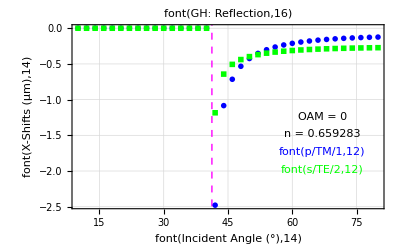

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->θloop Degree,k0->1,p->0,ℓ->0};

dat=Join[R1x$plotdata,R2x$plotdata]

p$Rxspin=ListLinePlot[{R1x$plotdata,R2x$plotdata},PlotMarkers->{{Graphics[Disk[]],.03},{Graphics[Rectangle[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["X-Shifts (μm)",14]},PlotLabel->font["GH: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


θcrit = ArcSin[n]/Degree /.params$here;
p$crit=Graphics[{Magenta,Dashing->Small,Line[{{θcrit,-5},{θcrit,5}}]}];


p$Rxspinfinal = Show[p$Rxspin,p$crit,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.4(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["p/TM/1",12],{67,vmin + 0.3(vmax-vmin)}]},Background->White],
Graphics[{Green,Text[font["s/TE/2",12],{67,vmin + 0.2(vmax-vmin)}]},Background->White]
]
```

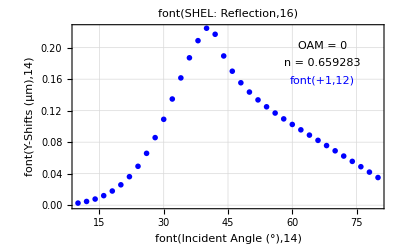

```mathematica
dat=R3y$plotdata;

p$Ryspin=ListLinePlot[dat,PlotMarkers->{Graphics[Disk[]],.03},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{{Thickness[.006],Blue},{Thickness[.006],Green},Darker[Red]},FrameLabel->{font["Incident Angle (°)",14],font["Y-Shifts (μm)",14]},PlotLabel->font["SHEL: Reflection",16]];

vmax= Max[Transpose[dat][[2]]];
vmin= Min[Transpose[dat][[2]]];


p$Ryspinfinal = Show[p$Ryspin,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{67,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{67,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font["+1",12],{67,vmin + 0.7(vmax-vmin)}]},Background->White]
]
```

#### Construction of Artmann Formula for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1$Art,R2$Art,β$Art,n];

R2$Art=(Cos[β$Art]-√(n^2-Sin[β$Art]^2))/(Cos[β$Art]+√(n^2-Sin[β$Art]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1$Art=(-n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2))/(n^2 Cos[β$Art]+√(n^2-Sin[β$Art]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β$Art_,n_]=FullSimplify[ArcTan[Re[R1],Im[R1]]];

Φ2[β$Art_,n_]=FullSimplify[ArcTan[Re[R2 ],Im[R2]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2,k0];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

#### Comparison with Artmann Formula for GH Shift

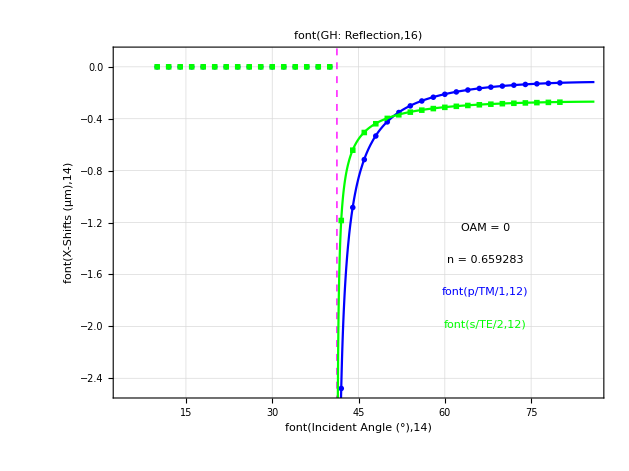

```mathematica
p$GH$analytic=Plot[{GHshift$1[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9),GHshift$2[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9)},{θ ,4,86},PlotStyle->{{Blue},{Green}},PlotRange->All];

p$GH=Show[p$Rxspinfinal,p$GH$analytic,PlotRange->{{4,86},{-2.5,0.1}},AspectRatio->0.75]
```

```mathematica
GHshift$1[44Degree,1/1.5168]/.k0->2π/(632.8*10^-9)

GHshift$2[44 Degree,1/1.5168]/.k0->2π/(632.8*10^-9)
```

-1.07862×10^-6

-6.39346×10^-7

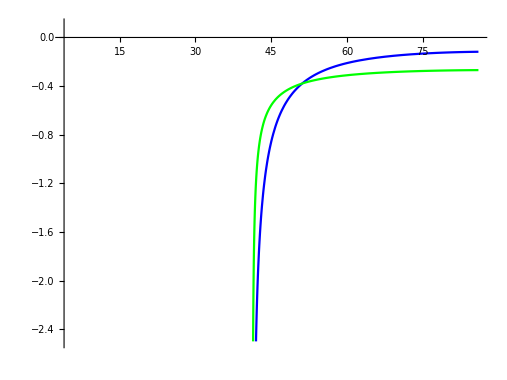

```mathematica
p$GH$analytic=Plot[{GHshift$1[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9),GHshift$2[θ Degree,1/1.5168]*10^6 /. k0->2π/(632.8*10^-9)},{θ ,4,86},PlotStyle->{{Blue},{Green}},PlotRange->{{4,86},{-2.5,0.1}},AspectRatio->0.75]
```

```mathematica
κvec = {κx ,κy,√(1-κx^2-κy^2)};

nvec = {-Sin[θ],0,Cos[θ]};
Clear[R1,R2,β,n];
β =ArcCos[κvec.nvec];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[β]-√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)
Plot3D[R2/.{n->.6592,θ->30*π/180},{κx,0,1},{κy,0,1},PlotRange->All]
```

-Graphics3D-